# QED calculation: Peskin Sec. 5

## e^+e^-→μ^+μ^- (QED): Peskin P.131-136

-Graphics-

### Initialization

You should choose English to avoid unnecessary confusions.

```mathematica
Exit[];
```

```mathematica
$Language="English";
```

```mathematica
<<FeynArts`
<<FormCalc`
```

FeynArts 3.9

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

last revised 2 Dec 14

FormCalc 8.4

by Thomas Hahn

last revised 5 Nov 14

$CharacterEncoding::utf8: The byte sequence {160} could not be interpreted as a character in the UTF-8 character encoding.

### Create Topology

TopologyList[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][5]],Propagator[Incoming][Vertex[1][2],Vertex[4][5]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5]],Propagator[Outgoing][Vertex[1][4],Vertex[4][5]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][5]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][5]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]]]

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

> Top. 4: 1 diagram

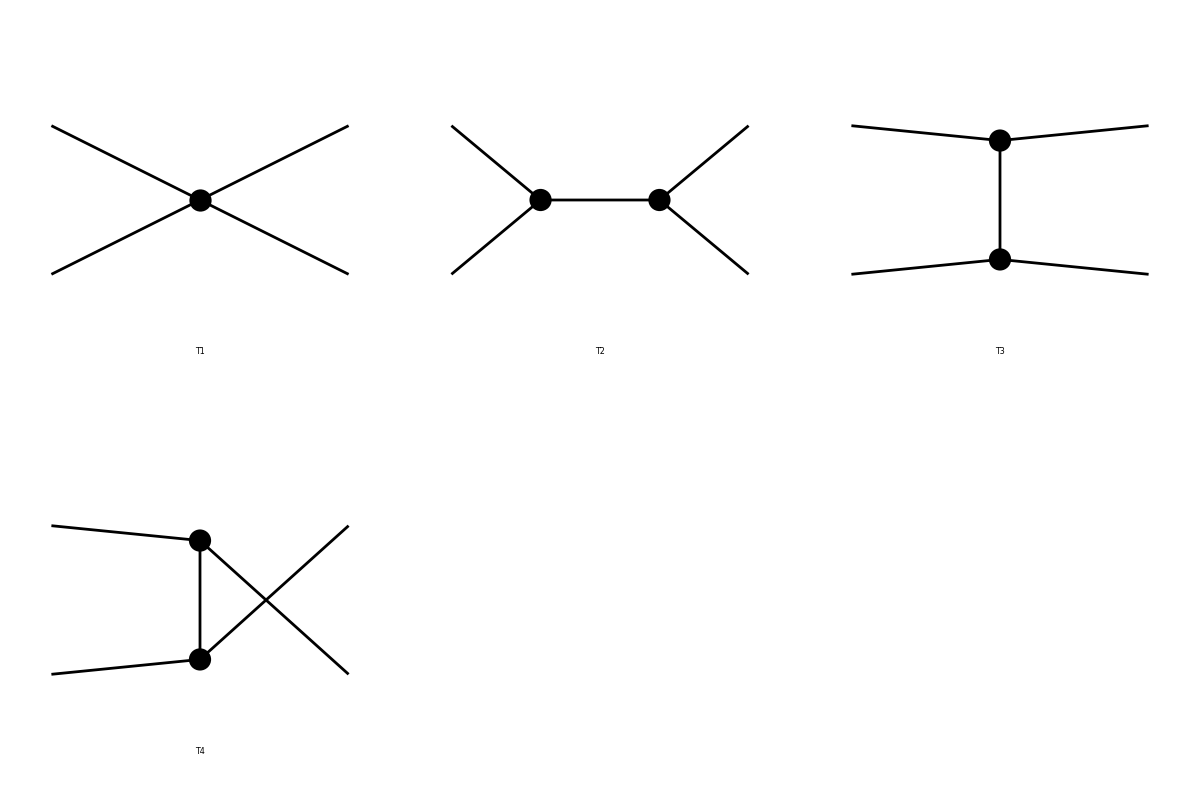

FeynArtsGraphics[2→2][([T1] | [T2] | [T3]
[T4] | Null | Null
Null | Null | Null)]

```mathematica
topologies=CreateTopologies[0,2->2]
Paint[topologies]
```

### Insert Particles

Manual P.74 has a list of the particles in the (default) SM model.

```mathematica
diagrams=InsertFields[topologies,{F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]},InsertionLevel->{Classes}]
```

loading generic model file /Users/misho/Documents/Mathematica/lib/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/Documents/Mathematica/lib/FeynArts/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counter terms of order 1

> 6 counter terms of order 2

classes model {SM} initialized

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 4 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

in total: 4 Classes insertions

TopologyList[Process→{F[2,{1}],-F[2,{1}]}→{F[2,{2}],-F[2,{2}]},Model→{SM},GenericModel→{Lorentz},InsertionLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][6],Field[5]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→S]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→S[1]],FeynmanGraph[1,Classes==2][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→S[2]]],FeynmanGraph[1,Generic==2][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→V]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→V[1]],FeynmanGraph[1,Classes==2][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→V[2]]]]]

> Top. 1: 4 diagrams

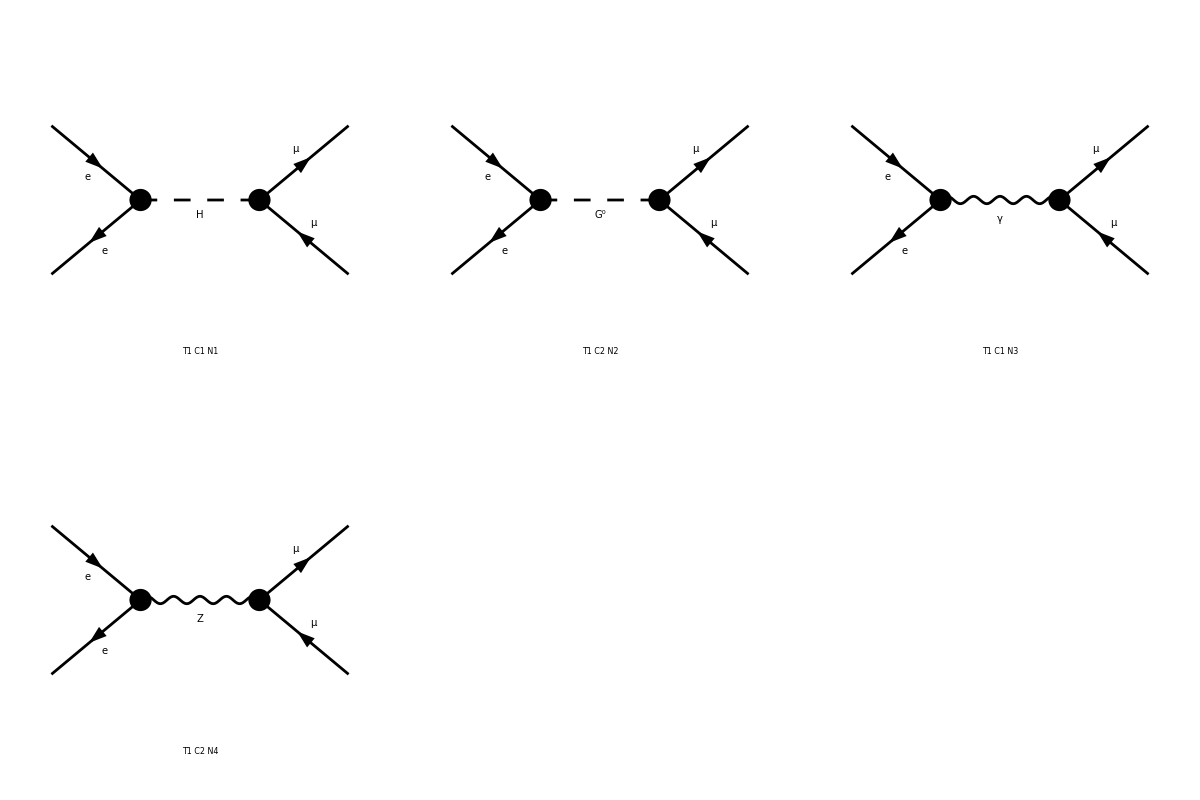

FeynArtsGraphics[{e,e}→{\mu,\mu}][([T1 C1 N1] | [T1 C2 N2] | [T1 C1 N3]
[T1 C2 N4] | Null | Null
Null | Null | Null)]

```mathematica
Paint[diagrams]
```

### Insert Particles (again...)

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 1 Classes insertion

> Top. 1: 1 diagram

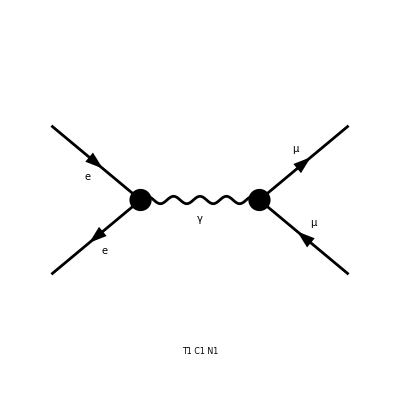

```mathematica
(* We concentrate on QED for simplicity. *)
diagrams=InsertFields[topologies,{F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]},InsertionLevel->{Classes},
	ExcludeParticles->{V[2],S[1],S[2]}];
Paint[diagrams];
```

### Pass the diagram to FormCalc

```mathematica
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams],FermionChains->VA];
matrix=SquaredME[amplitude]//.HelicityME[amplitude]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM... running FORM...

ok

> 1 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

ok

16 Alfa2 π^2 Den[S,0]^2 (1/2 (T^2+2 (ME2^2+MM2^2+MM2 (S-T-U)+ME2 (2 MM2+S-T-U))+U^2)+Hel[1] ((Abb16-2 ME2 (Abb1+MM2 Pair18)) Hel[2]+2 Abb18 ME MM Hel[3])+(Abb17-2 MM2 (Abb3+ME2 Pair17)-1/2 (Abb15-2 Abb12 ME2+2 (Abb13-2 Abb14 ME2) MM2) Hel[1] Hel[2]) Hel[3] Hel[4]+2 ME MM (Abb19 Hel[2] Hel[3]+(Abb20 Hel[1]+Abb21 Hel[2]) Hel[4]))

```mathematica
(* Assumes unpolarized fermions *)
matrix = matrix//.Hel[_]->0
```

8 Alfa2 π^2 (T^2+2 (ME2^2+MM2^2+MM2 (S-T-U)+ME2 (2 MM2+S-T-U))+U^2) Den[S,0]^2

-Graphics-

```mathematica
matrix//.Subexpr[]//.{Den[p2_,m2_]:>1/(p2-m2),Alfa->e^2/(4π),Alfa2->(e^2/(4π))^2,ME2->0}
```

(e^4 (T^2+2 (MM2^2+MM2 (S-T-U))+U^2))/(2 S^2)

```mathematica
%//.{S->4 EE^2,T->MM^2-2(EE^2-EE √(EE^2-MM^2)CosTheta),U->-S-T+2MM2}
```

(e^4 ((-2 (EE^2-CosTheta EE √(EE^2-MM2))+MM2)^2+(-4 EE^2+2 (EE^2-CosTheta EE √(EE^2-MM2))+MM2)^2+2 ((8 EE^2-2 MM2) MM2+MM2^2)))/(32 EE^4)

```mathematica
Collect[FullSimplify[%],{e,CosTheta}]
```

e^4 ((CosTheta^2 (EE^2-MM2))/(4 EE^2)+(EE^2+MM2)/(4 EE^2))

Many Traps!!!!!!!!!!!!!!!!

### Doing again with pacience.

```mathematica
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams],FermionChains->Weyl](*Default*)
amplitude//.Abbr[]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{F[2,{2}],k[3],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[4],MM,{Charge,-LeptonNumber}}}][-8 Alfa π Sub1 Den[S,0]]

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{F[2,{2}],k[3],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[4],MM,{Charge,-LeptonNumber}}}][-8 Alfa π Sub1 Den[S,0]]

```mathematica
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams],FermionChains->Chiral]
amplitude//.Abbr[]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{F[2,{2}],k[3],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[4],MM,{Charge,-LeptonNumber}}}][-4 Alfa π Den[S,0] Mat[F1]-4 Alfa π Den[S,0] Mat[F2]-4 Alfa π Den[S,0] Mat[F3]-4 Alfa π Den[S,0] Mat[F4]]

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{F[2,{2}],k[3],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[4],MM,{Charge,-LeptonNumber}}}][-4 Alfa π Den[S,0] Mat[(<v1|6,Lor[1]|u2>) (<u3|6,Lor[1]|v4>)]-4 Alfa π Den[S,0] Mat[(<v1|7,Lor[1]|u2>) (<u3|6,Lor[1]|v4>)]-4 Alfa π Den[S,0] Mat[(<v1|6,Lor[1]|u2>) (<u3|7,Lor[1]|v4>)]-4 Alfa π Den[S,0] Mat[(<v1|7,Lor[1]|u2>) (<u3|7,Lor[1]|v4>)]]

```mathematica
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams],FermionChains->VA]
amplitude//.Abbr[]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{F[2,{2}],k[3],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[4],MM,{Charge,-LeptonNumber}}}][-4 Alfa π Den[S,0] Mat[F1]]

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{F[2,{2}],k[3],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[4],MM,{Charge,-LeptonNumber}}}][-4 Alfa π Den[S,0] Mat[(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>)]]

```mathematica
SquaredME[amplitude]
```

16 Alfa2 π^2 Den[S,0]^2 Mat[F1,F1]

```mathematica
SquaredHelicityME=SquaredME[amplitude]//.HelicityME[amplitude]//.Abbr[]
```

> 1 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

16 Alfa2 π^2 Den[S,0]^2 (1/2 (T^2+2 (ME2^2+MM2^2+MM2 (S-T-U)+ME2 (2 MM2+S-T-U))+U^2)+Hel[1] (Hel[2] (-(ME2^2+MM2^2-T U) Pair[s[1],s[2]]+2 (Pair[s[1],k[3]] ((-MM2+U) Pair[s[2],k[1]]+(-2 ME2+S) Pair[s[2],k[3]])+Pair[s[1],k[2]] (MM2 Pair[s[2],k[1]]+(-MM2+T) Pair[s[2],k[3]]))-2 ME2 (MM2 Pair[s[1],s[2]]+Pair[s[1],k[4]] Pair[s[2],k[3]]+Pair[s[1],k[3]] Pair[s[2],k[4]]))+2 ME MM Hel[3] (-S Pair[s[1],s[3]]+Pair[s[1],k[2]] Pair[s[3],k[4]]))+2 ME MM (Hel[2] Hel[3] (-S Pair[s[2],s[3]]+Pair[s[2],k[1]] Pair[s[3],k[4]])+Hel[4] (Hel[1] (-S Pair[s[1],s[4]]+Pair[s[1],k[2]] Pair[s[4],k[3]])+Hel[2] (-S Pair[s[2],s[4]]+Pair[s[2],k[1]] Pair[s[4],k[3]])))+Hel[3] Hel[4] (-(ME2^2+MM2^2-T U) Pair[s[3],s[4]]-2 MM2 (ME2 Pair[s[3],s[4]]+Pair[s[3],k[2]] Pair[s[4],k[1]]+Pair[s[3],k[1]] Pair[s[4],k[2]])+2 (Pair[s[3],k[4]] ((-ME2+T) Pair[s[4],k[1]]+ME2 Pair[s[4],k[3]])+Pair[s[3],k[1]] ((-2 MM2+S) Pair[s[4],k[1]]+(-ME2+U) Pair[s[4],k[3]]))-1/2 Hel[1] Hel[2] ((2 ME2-S) (-2 MM2+S) Pair[s[1],s[4]] Pair[s[2],s[3]]+(2 ME2-S) (-2 MM2+S) Pair[s[1],s[3]] Pair[s[2],s[4]]+2 Pair[s[2],s[4]] ((-2 ME2+S) Pair[s[1],k[3]] Pair[s[3],k[4]]+Pair[s[1],k[2]] ((-2 MM2+S) Pair[s[3],k[1]]-(ME2+MM2-T) Pair[s[3],k[4]]))+2 Pair[s[1],s[4]] ((-2 ME2+S) Pair[s[2],k[3]] Pair[s[3],k[4]]+Pair[s[2],k[1]] ((-2 MM2+S) Pair[s[3],k[2]]-(ME2+MM2-U) Pair[s[3],k[4]]))+(-2 ME2^2-2 MM2^2+T^2+4 T U+U^2-2 MM2 (T+U)+ME2 (4 MM2-2 (T+U))) Pair[s[1],s[2]] Pair[s[3],s[4]]-2 (Pair[s[1],k[4]] (-(ME2+MM2-U) Pair[s[2],k[1]]+(-2 ME2+S) Pair[s[2],k[3]])+Pair[s[1],k[3]] (-(ME2+MM2-T) Pair[s[2],k[1]]+(-2 ME2+S) Pair[s[2],k[4]])-Pair[s[1],k[2]] ((4 MM2-2 S) Pair[s[2],k[1]]+(ME2+MM2-U) Pair[s[2],k[3]]+(ME2+MM2-T) Pair[s[2],k[4]])) Pair[s[3],s[4]]+2 Pair[s[1],s[3]] ((-2 ME2+S) Pair[s[2],k[4]] Pair[s[4],k[3]]+Pair[s[2],k[1]] ((-2 MM2+S) Pair[s[4],k[2]]-(ME2+MM2-T) Pair[s[4],k[3]]))+2 Pair[s[2],s[3]] ((-2 ME2+S) Pair[s[1],k[4]] Pair[s[4],k[3]]+Pair[s[1],k[2]] ((-2 MM2+S) Pair[s[4],k[1]]-(ME2+MM2-U) Pair[s[4],k[3]]))-2 Pair[s[1],s[2]] (-Pair[s[3],k[4]] ((ME2+MM2-U) Pair[s[4],k[1]]+(ME2+MM2-T) Pair[s[4],k[2]]+2 (2 ME2-S) Pair[s[4],k[3]])+Pair[s[3],k[1]] ((-2 MM2+S) Pair[s[4],k[2]]-(ME2+MM2-T) Pair[s[4],k[3]])+Pair[s[3],k[2]] ((-2 MM2+S) Pair[s[4],k[1]]-(ME2+MM2-U) Pair[s[4],k[3]]))-2 (MM2 ((-2 ME2+S) Pair[s[1],s[4]] Pair[s[2],s[3]]+(-2 ME2+S) Pair[s[1],s[3]] Pair[s[2],s[4]]+2 ME2 (Pair[s[1],s[4]] Pair[s[2],s[3]]+Pair[s[1],s[3]] Pair[s[2],s[4]])-2 Pair[s[1],k[2]] Pair[s[2],s[4]] Pair[s[3],k[1]]-2 Pair[s[1],s[4]] Pair[s[2],k[1]] Pair[s[3],k[2]]+(2 ME2-S) Pair[s[1],s[2]] Pair[s[3],s[4]]+2 Pair[s[1],k[2]] Pair[s[2],k[1]] Pair[s[3],s[4]]-2 Pair[s[1],k[2]] Pair[s[2],s[3]] Pair[s[4],k[1]]-2 Pair[s[1],s[3]] Pair[s[2],k[1]] Pair[s[4],k[2]]+2 Pair[s[1],s[2]] (Pair[s[3],k[2]] Pair[s[4],k[1]]+Pair[s[3],k[1]] Pair[s[4],k[2]]))+ME2 ((-2 MM2+S) Pair[s[1],s[4]] Pair[s[2],s[3]]+(-2 MM2+S) Pair[s[1],s[3]] Pair[s[2],s[4]]-2 Pair[s[1],s[4]] Pair[s[2],k[3]] Pair[s[3],k[4]]-2 Pair[s[1],k[3]] Pair[s[2],s[4]] Pair[s[3],k[4]]+(2 MM2-S) Pair[s[1],s[2]] Pair[s[3],s[4]]+2 (Pair[s[1],k[4]] Pair[s[2],k[3]]+Pair[s[1],k[3]] Pair[s[2],k[4]]) Pair[s[3],s[4]]-2 Pair[s[1],s[3]] Pair[s[2],k[4]] Pair[s[4],k[3]]-2 Pair[s[1],k[4]] Pair[s[2],s[3]] Pair[s[4],k[3]]+2 Pair[s[1],s[2]] Pair[s[3],k[4]] Pair[s[4],k[3]]))+4 (-Pair[s[2],k[1]] (Pair[s[1],k[3]] Pair[s[3],k[4]] Pair[s[4],k[2]]+Pair[s[1],k[4]] Pair[s[3],k[2]] Pair[s[4],k[3]])-Pair[s[1],k[2]] (Pair[s[2],k[3]] Pair[s[3],k[4]] Pair[s[4],k[1]]+(Pair[s[2],k[4]] Pair[s[3],k[1]]-2 Pair[s[2],k[1]] Pair[s[3],k[4]]) Pair[s[4],k[3]])))))

```mathematica
SquaredHelicityME//.{Hel[1]->0,Hel[2]->0,Hel[3]->0,Hel[4]->0}
```

8 Alfa2 π^2 (T^2+2 (ME2^2+MM2^2+MM2 (S-T-U)+ME2 (2 MM2+S-T-U))+U^2) Den[S,0]^2

This is AVERAGE! So we have to multiply by four.

```mathematica
MatrixElement=2^2*(SquaredHelicityME//.{Hel[_]->0})
```

32 Alfa2 π^2 (T^2+2 (ME2^2+MM2^2+MM2 (S-T-U)+ME2 (2 MM2+S-T-U))+U^2) Den[S,0]^2

```mathematica
MatrixElement//.Subexpr[]//.{Den[p2_,m2_]:>1/(p2-m2),Alfa->e^2/(4π),Alfa2->(e^2/(4π))^2,ME2->0}//.{S->4 EE^2,T->MM^2-2(EE^2-EE √(EE^2-MM^2)CosTheta),U->-T-S+2MM2}
```

(e^4 ((-2 (EE^2-CosTheta EE √(EE^2-MM2))+MM2)^2+(-4 EE^2+2 (EE^2-CosTheta EE √(EE^2-MM2))+MM2)^2+2 ((8 EE^2-2 MM2) MM2+MM2^2)))/(8 EE^4)

```mathematica
Collect[FullSimplify[%],{e,CosTheta}]
```

e^4 ((CosTheta^2 (EE^2-MM2))/EE^2+(EE^2+MM2)/EE^2)

-Graphics-